## Calculate the elongation of the nuclear axes

### The elongation is considered along one of the tree principal axes of the rotational ellipsoid.

```mathematica
rk[beta_,gamma_,k_]:=Sqrt[5/(4π)]beta*Cos[gamma*π/180-(2π*k)/3];
```

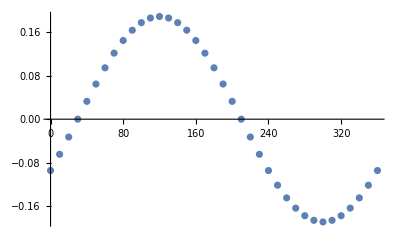

```mathematica
t1=Table[{x,rk[0.3,x,1]},{x,0,360,10}];
ListPlot[t1]
```